# Matrix Numerov Method to Estimate Wavefunctions Numerically

## Madeleine Sutherland November 2018

#### Developing a Matrix Numerov Method and Testing it on the Linear Potential:

I referred to the Wikipedia derivation, another derivation1, and a prior paper on Mathematica implementation2, though I chose to differ from the author by not using scaled variables because they’re annoying.

Let the potential function be V(x) = a |x| where:

```mathematica
a=5.368244090805358*^-9
```

5.36824×10^-9

This potential has eigen-energies which can be calculated from the Airy functions; the first ten are:

```mathematica
knownEigenEs={1.1346507841823254*^-16,2.603998536121299*^-16,3.617584765862314*^-16,4.55283376658974*^-16,5.368244090805356*^-16,6.148361553716667*^-16,6.864202756448613*^-16,7.558497035922867*^-16,8.21054614270103*^-16,8.847545728255032*^-16}
```

{1.13465×10^-16,2.604×10^-16,3.61758×10^-16,4.55283×10^-16,5.36824×10^-16,6.14836×10^-16,6.8642×10^-16,7.5585×10^-16,8.21055×10^-16,8.84755×10^-16}

I need to define a grid spacing appropriate for this problem. I need to be sure that for the resulting wavefunctions, I have at least five or so points per lobe. I know from the de Broglie relation λ=h/p that the wavelength λ will be the smallest where momentum p is the largest; that will be at the minimum potential energy, in this case at x=0 where V=0. There, p=(2 m E)^(-1/2). I will follow the recommendations in the paper cited and use the highest E value I want to reliably predict a wavefunction for, 8.84755×10^-16. (For this quantum problem the reduced mass of the particle was 1.16×10^-23.

```mathematica
m
```

1.16×10^-23

```mathematica
p0=(2 m 8.847545728255032*^-16)^(1/2)
```

1.4327×10^-19

```mathematica
h/p0
```

4.62488×10^-8

```mathematica
(0.5*(h/p0))/5
```

4.62488×10^-9

```mathematica
dx=4.624881629283604*^-9
```

4.62488×10^-9

Then it was time to find the left and write bounds; wavefunctions eventually approach zero as the potential gets higher and higher, so I just need to go a short distance outside the “turning points” where the total E = the potential, v1. I will go two λ0’s outside on each end, allowing me to define my x grid below:

```mathematica
v1
```

5.36824×10^-9 Abs[x]

```mathematica
xvals=Table[i,{i,(-1.6481265714815332*^-7)-2 λ0,(1.6481265714815332*^-7)+2 λ0,dx}]
```

{-2.5731×10^-7,-2.52685×10^-7,-2.48061×10^-7,-2.43436×10^-7,-2.38811×10^-7,-2.34186×10^-7,-2.29561×10^-7,-2.24936×10^-7,-2.20311×10^-7,-2.15686×10^-7,-2.11061×10^-7,-2.06437×10^-7,-2.01812×10^-7,-1.97187×10^-7,-1.92562×10^-7,-1.87937×10^-7,-1.83312×10^-7,-1.78687×10^-7,-1.74062×10^-7,-1.69438×10^-7,-1.64813×10^-7,-1.60188×10^-7,-1.55563×10^-7,-1.50938×10^-7,-1.46313×10^-7,-1.41688×10^-7,-1.37063×10^-7,-1.32438×10^-7,-1.27814×10^-7,-1.23189×10^-7,-1.18564×10^-7,-1.13939×10^-7,-1.09314×10^-7,-1.04689×10^-7,-1.00064×10^-7,-9.54394×10^-8,-9.08146×10^-8,-8.61897×10^-8,-8.15648×10^-8,-7.69399×10^-8,-7.2315×10^-8,-6.76901×10^-8,-6.30653×10^-8,-5.84404×10^-8,-5.38155×10^-8,-4.91906×10^-8,-4.45657×10^-8,-3.99409×10^-8,-3.5316×10^-8,-3.06911×10^-8,-2.60662×10^-8,-2.14413×10^-8,-1.68164×10^-8,-1.21916×10^-8,-7.56668×10^-9,-2.9418×10^-9,1.68308×10^-9,6.30796×10^-9,1.09328×10^-8,1.55577×10^-8,2.01826×10^-8,2.48075×10^-8,2.94324×10^-8,3.40573×10^-8,3.86821×10^-8,4.3307×10^-8,4.79319×10^-8,5.25568×10^-8,5.71817×10^-8,6.18065×10^-8,6.64314×10^-8,7.10563×10^-8,7.56812×10^-8,8.03061×10^-8,8.4931×10^-8,8.95558×10^-8,9.41807×10^-8,9.88056×10^-8,1.0343×10^-7,1.08055×10^-7,1.1268×10^-7,1.17305×10^-7,1.2193×10^-7,1.26555×10^-7,1.3118×10^-7,1.35805×10^-7,1.4043×10^-7,1.45054×10^-7,1.49679×10^-7,1.54304×10^-7,1.58929×10^-7,1.63554×10^-7,1.68179×10^-7,1.72804×10^-7,1.77429×10^-7,1.82053×10^-7,1.86678×10^-7,1.91303×10^-7,1.95928×10^-7,2.00553×10^-7,2.05178×10^-7,2.09803×10^-7,2.14428×10^-7,2.19053×10^-7,2.23677×10^-7,2.28302×10^-7,2.32927×10^-7,2.37552×10^-7,2.42177×10^-7,2.46802×10^-7,2.51427×10^-7,2.56052×10^-7}

```mathematica
Dimensions[%]
```

{112}

```mathematica
v1input[x_]=a Abs[x]
```

5.36824×10^-9 Abs[x]

```mathematica
v1input[1.6481265714815332*^-7]
```

8.84755×10^-16

Now I will construct my V matrix from the value of the potential function evaluated at each of the x grid points:

```mathematica
Vvals=v1input[xvals]
```

{1.3813×10^-15,1.35648×10^-15,1.33165×10^-15,1.30682×10^-15,1.28199×10^-15,1.25717×10^-15,1.23234×10^-15,1.20751×10^-15,1.18268×10^-15,1.15786×10^-15,1.13303×10^-15,1.1082×10^-15,1.08337×10^-15,1.05855×10^-15,1.03372×10^-15,1.00889×10^-15,9.84065×10^-16,9.59237×10^-16,9.3441×10^-16,9.09582×10^-16,8.84755×10^-16,8.59927×10^-16,8.351×10^-16,8.10272×10^-16,7.85445×10^-16,7.60617×10^-16,7.3579×10^-16,7.10962×10^-16,6.86135×10^-16,6.61307×10^-16,6.3648×10^-16,6.11652×10^-16,5.86825×10^-16,5.61997×10^-16,5.3717×10^-16,5.12342×10^-16,4.87515×10^-16,4.62687×10^-16,4.3786×10^-16,4.13032×10^-16,3.88205×10^-16,3.63377×10^-16,3.3855×10^-16,3.13722×10^-16,2.88895×10^-16,2.64067×10^-16,2.3924×10^-16,2.14412×10^-16,1.89585×10^-16,1.64757×10^-16,1.3993×10^-16,1.15102×10^-16,9.02748×10^-17,6.54473×10^-17,4.06198×10^-17,1.57923×10^-17,9.03519×10^-18,3.38627×10^-17,5.86902×10^-17,8.35177×10^-17,1.08345×10^-16,1.33173×10^-16,1.58×10^-16,1.82828×10^-16,2.07655×10^-16,2.32483×10^-16,2.5731×10^-16,2.82138×10^-16,3.06965×10^-16,3.31793×10^-16,3.5662×10^-16,3.81448×10^-16,4.06275×10^-16,4.31103×10^-16,4.5593×10^-16,4.80758×10^-16,5.05585×10^-16,5.30413×10^-16,5.5524×10^-16,5.80068×10^-16,6.04895×10^-16,6.29723×10^-16,6.5455×10^-16,6.79378×10^-16,7.04205×10^-16,7.29033×10^-16,7.5386×10^-16,7.78687×10^-16,8.03515×10^-16,8.28342×10^-16,8.5317×10^-16,8.77997×10^-16,9.02825×10^-16,9.27652×10^-16,9.5248×10^-16,9.77307×10^-16,1.00213×10^-15,1.02696×10^-15,1.05179×10^-15,1.07662×10^-15,1.10144×10^-15,1.12627×10^-15,1.1511×10^-15,1.17593×10^-15,1.20075×10^-15,1.22558×10^-15,1.25041×10^-15,1.27524×10^-15,1.30006×10^-15,1.32489×10^-15,1.34972×10^-15,1.37455×10^-15}

```mathematica
Dimensions[Vvals]
```

{112}

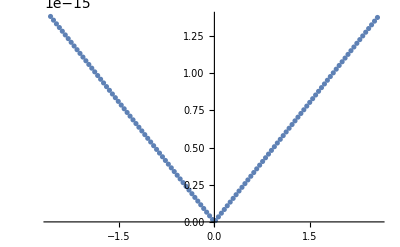

```mathematica
ListPlot[Transpose[{xvals,Vvals}]]
```

I will now use the Matrix Numerov method as described in the Wisconsin paper I cited, except that I won’t bother with scaled variables:

```mathematica
n1=112
```

112

```mathematica
one[n1_,d_]:=DiagonalMatrix[1+0 Range[n1-Abs[d]],d](*this creates a matrix with 1's along the d'th diagonal and total dimensions n1*n1 as required. This is mainly what I got out of the Wisconsin paper*)
```

```mathematica
one[10,1]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Dimensions[%]
```

{10,10}

```mathematica
one[n1,-1]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}

```mathematica
Dimensions[%]
```

{112,112}

```mathematica
B=(one[n1,-1]+10 one[n1,0]+one[n1,1])/12.
```

{{0.833333,0.0833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},110,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,86,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0833333,0.833333}}
 |  |  |  |

```mathematica
Dimensions[B]
```

{112,112}

```mathematica
A=(one[n1,-1]-2 one[n1,0]+one[n1,1])/((dx)^2)
```

{{-9.35037×10^16,4.67518×10^16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},110,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,89,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.67518×10^16,-9.35037×10^16}}
 |  |  |  |

```mathematica
Dimensions[A]
```

{112,112}

```mathematica
KE=(-ℏ^2/(2 m))*Inverse[B].A
```

{{5.708×10^-15,-3.2934×10^-15,3.32701×10^-16,-3.36096×10^-17,3.39526×10^-18,-3.42991×10^-19,101,-9.66184×10^-121,9.76044×10^-122,-9.86003×10^-123,9.95963×10^-124,-9.95963×10^-125},110,{1}}
 |  |  |  |

```mathematica
Dimensions[KE]
```

{112,112}

```mathematica
V=DiagonalMatrix[Vvals]
```

{1}
 |  |  |  |

```mathematica
Dimensions[V]
```

{112,112}

```mathematica
H1=KE+V
```

{{7.08931×10^-15,-3.2934×10^-15,3.32701×10^-16,-3.36096×10^-17,3.39526×10^-18,-3.42991×10^-19,101,-9.66184×10^-121,9.76044×10^-122,-9.86003×10^-123,9.95963×10^-124,-9.95963×10^-125},110,{1}}
 |  |  |  |

```mathematica
Dimensions[H1]
```

{112,112}

Now I have constructed my Hamiltonian I can use it - time to solve for the eigenvalues (energies of the particle in this potential) and eigenvectors (discretized wavefunctions, which we can plot and characterize!).

```mathematica
{energies1,vectors1}=Eigensystem[H1]
```

{{1.45125×10^-14,1.45058×10^-14,1.42591×10^-14,1.42524×10^-14,1.40525×10^-14,1.40458×10^-14,100,6.14806×10^-16,5.36843×10^-16,4.5527×10^-16,3.61808×10^-16,2.60396×10^-16,1.13641×10^-16},{1}}
 |  |  |  |

```mathematica
energies1
```

{1.45125×10^-14,1.45058×10^-14,1.42591×10^-14,1.42524×10^-14,1.40525×10^-14,1.40458×10^-14,1.38705×10^-14,1.38637×10^-14,1.37049×10^-14,1.36978×10^-14,1.356×10^-14,1.35362×10^-14,1.34252×10^-14,1.33578×10^-14,1.32502×10^-14,1.31522×10^-14,1.30353×10^-14,1.29193×10^-14,1.27912×10^-14,1.26614×10^-14,1.25226×10^-14,1.23812×10^-14,1.22325×10^-14,1.2081×10^-14,1.19234×10^-14,1.1763×10^-14,1.15976×10^-14,1.14295×10^-14,1.12572×10^-14,1.10826×10^-14,1.09043×10^-14,1.07241×10^-14,1.0541×10^-14,1.03563×10^-14,1.01691×10^-14,9.98082×10^-15,9.79064×10^-15,9.59968×10^-15,9.40736×10^-15,9.21462×10^-15,9.02099×10^-15,8.8273×10^-15,8.63318×10^-15,8.43934×10^-15,8.24548×10^-15,8.05222×10^-15,7.85933×10^-15,7.66734×10^-15,7.47609×10^-15,7.28601×10^-15,7.097×10^-15,6.90943×10^-15,6.72323×10^-15,6.53871×10^-15,6.35584×10^-15,6.17486×10^-15,5.99578×10^-15,5.81879×10^-15,5.64394×10^-15,5.47135×10^-15,5.30111×10^-15,5.13329×10^-15,4.968×10^-15,4.80527×10^-15,4.64525×10^-15,4.48791×10^-15,4.33343×10^-15,4.18173×10^-15,4.03304×10^-15,3.88723×10^-15,3.74454×10^-15,3.60481×10^-15,3.46833×10^-15,3.33486×10^-15,3.20476×10^-15,3.07773×10^-15,2.95416×10^-15,2.83372×10^-15,2.71684×10^-15,2.60313×10^-15,2.49308×10^-15,2.38625×10^-15,2.28318×10^-15,2.18338×10^-15,2.08746×10^-15,1.99487×10^-15,1.90629×10^-15,1.82114×10^-15,1.74016×10^-15,1.66274×10^-15,1.58968×10^-15,1.52033×10^-15,1.45542×10^-15,1.39402×10^-15,1.33639×10^-15,1.28081×10^-15,1.22688×10^-15,1.17261×10^-15,1.1181×10^-15,1.06187×10^-15,1.00475×10^-15,9.45301×10^-16,8.84669×10^-16,8.21013×10^-16,7.55796×10^-16,6.86411×10^-16,6.14806×10^-16,5.36843×10^-16,4.5527×10^-16,3.61808×10^-16,2.60396×10^-16,1.13641×10^-16}

```mathematica
first10energies=Take[energies1,-10](*Note that they're in descending order*)
```

{8.84669×10^-16,8.21013×10^-16,7.55796×10^-16,6.86411×10^-16,6.14806×10^-16,5.36843×10^-16,4.5527×10^-16,3.61808×10^-16,2.60396×10^-16,1.13641×10^-16}

These values are within 0.01% of the energies I calculated with Airy functions:

```mathematica
knownEigenEs={1.1346507841823254*^-16,2.603998536121299*^-16,3.617584765862314*^-16,4.55283376658974*^-16,5.368244090805356*^-16,6.148361553716667*^-16,6.864202756448613*^-16,7.558497035922867*^-16,8.21054614270103*^-16,8.847545728255032*^-16}
```

{1.13465×10^-16,2.604×10^-16,3.61758×10^-16,4.55283×10^-16,5.36824×10^-16,6.14836×10^-16,6.8642×10^-16,7.5585×10^-16,8.21055×10^-16,8.84755×10^-16}

```mathematica
knownEigenEs-Reverse[first10energies]
```

{-1.76002×10^-19,4.18749×10^-21,-4.98532×10^-20,1.33746×10^-20,-1.90294×10^-20,2.99306×10^-20,9.29781×10^-21,5.38992×10^-20,4.17202×10^-20,8.52875×10^-20}

```mathematica
(knownEigenEs-Reverse[first10energies])^2
```

{3.09766×10^-38,1.7535×10^-41,2.48534×10^-39,1.78879×10^-40,3.62116×10^-40,8.95839×10^-40,8.64493×10^-41,2.90512×10^-39,1.74057×10^-39,7.27397×10^-39}

Mean squared error:

```mathematica
Mean[%]
```

4.69225×10^-39

```mathematica
Abs[knownEigenEs-Reverse[first10energies]]
```

{1.76002×10^-19,4.18749×10^-21,4.98532×10^-20,1.33746×10^-20,1.90294×10^-20,2.99306×10^-20,9.29781×10^-21,5.38992×10^-20,4.17202×10^-20,8.52875×10^-20}

```mathematica
Mean[%]
```

4.82582×10^-20

#### Generalized Numerov-Cooley Code:

Having shown that this procedure works for the V potential, I decided to try and generalize it.
I’ve managed to write a Matrix Numerov function that’s plug-and-go. The only flaw is that you need to define your potential function somewhere else in your notebook with syntax like:

```mathematica
v1input[x_]=a Abs[x]
```

5.36824×10^-9 Abs[x]

... and then plug the name of the function (i.e. “v1function”) into the expr_ field of my MatrixNumerov function. My MatrixNumerov function takes arguments [potential, xmin_,xmax_,dx_, ℏ_, m_], the latter two allowing for you to put in hbar in your chosen units and mass of choice.

```mathematica
Vfunction[expr_,xmin_,xmax_,dx_]:=expr[Table[i,{i,xmin,xmax,dx}]]
```

```mathematica
Vfunction[v1input,(-1.6481265714815332*^-7)-2 λ0,(1.6481265714815332*^-7)+2 λ0,dx]
```

{1.3813×10^-15,1.35648×10^-15,1.33165×10^-15,1.30682×10^-15,1.28199×10^-15,1.25717×10^-15,1.23234×10^-15,1.20751×10^-15,1.18268×10^-15,1.15786×10^-15,1.13303×10^-15,1.1082×10^-15,1.08337×10^-15,1.05855×10^-15,1.03372×10^-15,1.00889×10^-15,9.84065×10^-16,9.59237×10^-16,9.3441×10^-16,9.09582×10^-16,8.84755×10^-16,8.59927×10^-16,8.351×10^-16,8.10272×10^-16,7.85445×10^-16,7.60617×10^-16,7.3579×10^-16,7.10962×10^-16,6.86135×10^-16,6.61307×10^-16,6.3648×10^-16,6.11652×10^-16,5.86825×10^-16,5.61997×10^-16,5.3717×10^-16,5.12342×10^-16,4.87515×10^-16,4.62687×10^-16,4.3786×10^-16,4.13032×10^-16,3.88205×10^-16,3.63377×10^-16,3.3855×10^-16,3.13722×10^-16,2.88895×10^-16,2.64067×10^-16,2.3924×10^-16,2.14412×10^-16,1.89585×10^-16,1.64757×10^-16,1.3993×10^-16,1.15102×10^-16,9.02748×10^-17,6.54473×10^-17,4.06198×10^-17,1.57923×10^-17,9.03519×10^-18,3.38627×10^-17,5.86902×10^-17,8.35177×10^-17,1.08345×10^-16,1.33173×10^-16,1.58×10^-16,1.82828×10^-16,2.07655×10^-16,2.32483×10^-16,2.5731×10^-16,2.82138×10^-16,3.06965×10^-16,3.31793×10^-16,3.5662×10^-16,3.81448×10^-16,4.06275×10^-16,4.31103×10^-16,4.5593×10^-16,4.80758×10^-16,5.05585×10^-16,5.30413×10^-16,5.5524×10^-16,5.80068×10^-16,6.04895×10^-16,6.29723×10^-16,6.5455×10^-16,6.79378×10^-16,7.04205×10^-16,7.29033×10^-16,7.5386×10^-16,7.78687×10^-16,8.03515×10^-16,8.28342×10^-16,8.5317×10^-16,8.77997×10^-16,9.02825×10^-16,9.27652×10^-16,9.5248×10^-16,9.77307×10^-16,1.00213×10^-15,1.02696×10^-15,1.05179×10^-15,1.07662×10^-15,1.10144×10^-15,1.12627×10^-15,1.1511×10^-15,1.17593×10^-15,1.20075×10^-15,1.22558×10^-15,1.25041×10^-15,1.27524×10^-15,1.30006×10^-15,1.32489×10^-15,1.34972×10^-15,1.37455×10^-15}

```mathematica
Vmatrix[expr_,xmin_,xmax_,dx_]:=Module[{Vfunction,V},
Vfunction=expr[Table[i,{i,xmin,xmax,dx}]];
V=DiagonalMatrix[Vfunction];
V]
```

```mathematica
Vmatrix[v1input,(-1.6481265714815332*^-7)-2 λ0,(1.6481265714815332*^-7)+2 λ0,dx]
```

(1.3813×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.35648×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.33165×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.30682×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.28199×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1.25717×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.23234×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.20751×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.18268×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.15786×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13303×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.1082×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.08337×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.05855×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.03372×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.00889×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.84065×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.59237×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.3441×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.09582×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.84755×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.59927×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.351×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.10272×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.85445×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.60617×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.3579×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.10962×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.86135×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.61307×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.3648×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.11652×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.86825×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.61997×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.3717×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.12342×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.87515×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.62687×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.3786×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.13032×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.88205×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.63377×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.3855×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.13722×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.88895×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.64067×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.3924×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.14412×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.89585×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.64757×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.3993×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.15102×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.02748×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.54473×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.06198×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.57923×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.03519×10^-18 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.38627×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.86902×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.35177×10^-17 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.08345×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.33173×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.58×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.82828×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.07655×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.32483×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.5731×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.82138×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.06965×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.31793×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.5662×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.81448×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.06275×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.31103×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.5593×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.80758×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.05585×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.30413×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.5524×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.80068×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.04895×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.29723×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.5455×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.79378×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.04205×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.29033×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.5386×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.78687×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.03515×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.28342×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.5317×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.77997×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.02825×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.27652×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.5248×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.77307×10^-16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.00213×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.02696×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.05179×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.07662×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.10144×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.12627×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.1511×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.17593×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.20075×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.22558×10^-15 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.25041×10^-15 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.27524×10^-15 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.30006×10^-15 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.32489×10^-15 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.34972×10^-15 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.37455×10^-15)

```mathematica
Dimensions[%]
```

{112,112}

```mathematica
one[n_,d_]:=DiagonalMatrix[1+0 Range[n-Abs[d]],d]
```

```mathematica
KEoperator[n_,ℏ_,m_,dx_]:=Module[{B,A,KE},
B=(DiagonalMatrix[1+0 Range[n-Abs[-1]],-1]+10 DiagonalMatrix[1+0 Range[n-Abs[0]],0]+DiagonalMatrix[1+0 Range[n-Abs[1]],1])/12.;A=(DiagonalMatrix[1+0 Range[n-Abs[-1]],-1]-2 DiagonalMatrix[1+0 Range[n-Abs[0]],0]+DiagonalMatrix[1+0 Range[n-Abs[1]],1])/((dx)^2);KE=(-ℏ^2/(2 m))*Inverse[B].A;
	KE]
```

```mathematica
ℏ=1.0545718*10^(-27)
```

1.05457×10^-27

```mathematica
m=1.16*10^(-23)
```

1.16×10^-23

```mathematica
KE=(-ℏ^2/(2 m))*Inverse[B].A
```

(5.708×10^-15 | -3.2934×10^-15 | 3.32701×10^-16 | -3.36096×10^-17 | 3.39526×10^-18 | -3.42991×10^-19 | 3.46492×10^-20 | -3.50028×10^-21 | 3.536×10^-22 | -3.57208×10^-23 | 3.60853×10^-24 | -3.64536×10^-25 | 3.68256×10^-26 | -3.72014×10^-27 | 3.75811×10^-28 | -3.79646×10^-29 | 3.8352×10^-30 | -3.87434×10^-31 | 3.91388×10^-32 | -3.95382×10^-33 | 3.99417×10^-34 | -4.03493×10^-35 | 4.07611×10^-36 | -4.11771×10^-37 | 4.15973×10^-38 | -4.20218×10^-39 | 4.24506×10^-40 | -4.28838×10^-41 | 4.33215×10^-42 | -4.37636×10^-43 | 4.42102×10^-44 | -4.46614×10^-45 | 4.51171×10^-46 | -4.55776×10^-47 | 4.60427×10^-48 | -4.65126×10^-49 | 4.69872×10^-50 | -4.74667×10^-51 | 4.79511×10^-52 | -4.84405×10^-53 | 4.89348×10^-54 | -4.94342×10^-55 | 4.99387×10^-56 | -5.04483×10^-57 | 5.09632×10^-58 | -5.14833×10^-59 | 5.20087×10^-60 | -5.25394×10^-61 | 5.30756×10^-62 | -5.36172×10^-63 | 5.41644×10^-64 | -5.47172×10^-65 | 5.52756×10^-66 | -5.58396×10^-67 | 5.64095×10^-68 | -5.69852×10^-69 | 5.75667×10^-70 | -5.81542×10^-71 | 5.87477×10^-72 | -5.93472×10^-73 | 5.99528×10^-74 | -6.05647×10^-75 | 6.11827×10^-76 | -6.18071×10^-77 | 6.24379×10^-78 | -6.3075×10^-79 | 6.37187×10^-80 | -6.4369×10^-81 | 6.50259×10^-82 | -6.56895×10^-83 | 6.63599×10^-84 | -6.70371×10^-85 | 6.77212×10^-86 | -6.84123×10^-87 | 6.91105×10^-88 | -6.98157×10^-89 | 7.05282×10^-90 | -7.1248×10^-91 | 7.19751×10^-92 | -7.27096×10^-93 | 7.34516×10^-94 | -7.42012×10^-95 | 7.49584×10^-96 | -7.57234×10^-97 | 7.64961×10^-98 | -7.72768×10^-99 | 7.80654×10^-100 | -7.88621×10^-101 | 7.96669×10^-102 | -8.04799×10^-103 | 8.13012×10^-104 | -8.21309×10^-105 | 8.29691×10^-106 | -8.38158×10^-107 | 8.46711×10^-108 | -8.55352×10^-109 | 8.64081×10^-110 | -8.72899×10^-111 | 8.81807×10^-112 | -8.90806×10^-113 | 8.99897×10^-114 | -9.0908×10^-115 | 9.18358×10^-116 | -9.2773×10^-117 | 9.37197×10^-118 | -9.46762×10^-119 | 9.56423×10^-120 | -9.66184×10^-121 | 9.76044×10^-122 | -9.86003×10^-123 | 9.95963×10^-124 | -9.95963×10^-125
-3.2934×10^-15 | 6.0407×10^-15 | -3.32701×10^-15 | 3.36096×10^-16 | -3.39526×10^-17 | 3.42991×10^-18 | -3.46492×10^-19 | 3.50028×10^-20 | -3.536×10^-21 | 3.57208×10^-22 | -3.60853×10^-23 | 3.64536×10^-24 | -3.68256×10^-25 | 3.72014×10^-26 | -3.75811×10^-27 | 3.79646×10^-28 | -3.8352×10^-29 | 3.87434×10^-30 | -3.91388×10^-31 | 3.95382×10^-32 | -3.99417×10^-33 | 4.03493×10^-34 | -4.07611×10^-35 | 4.11771×10^-36 | -4.15973×10^-37 | 4.20218×10^-38 | -4.24506×10^-39 | 4.28838×10^-40 | -4.33215×10^-41 | 4.37636×10^-42 | -4.42102×10^-43 | 4.46614×10^-44 | -4.51171×10^-45 | 4.55776×10^-46 | -4.60427×10^-47 | 4.65126×10^-48 | -4.69872×10^-49 | 4.74667×10^-50 | -4.79511×10^-51 | 4.84405×10^-52 | -4.89348×10^-53 | 4.94342×10^-54 | -4.99387×10^-55 | 5.04483×10^-56 | -5.09632×10^-57 | 5.14833×10^-58 | -5.20087×10^-59 | 5.25394×10^-60 | -5.30756×10^-61 | 5.36172×10^-62 | -5.41644×10^-63 | 5.47172×10^-64 | -5.52756×10^-65 | 5.58396×10^-66 | -5.64095×10^-67 | 5.69852×10^-68 | -5.75667×10^-69 | 5.81542×10^-70 | -5.87477×10^-71 | 5.93472×10^-72 | -5.99528×10^-73 | 6.05647×10^-74 | -6.11827×10^-75 | 6.18071×10^-76 | -6.24379×10^-77 | 6.3075×10^-78 | -6.37187×10^-79 | 6.4369×10^-80 | -6.50259×10^-81 | 6.56895×10^-82 | -6.63599×10^-83 | 6.70371×10^-84 | -6.77212×10^-85 | 6.84123×10^-86 | -6.91105×10^-87 | 6.98157×10^-88 | -7.05282×10^-89 | 7.1248×10^-90 | -7.19751×10^-91 | 7.27096×10^-92 | -7.34516×10^-93 | 7.42012×10^-94 | -7.49584×10^-95 | 7.57234×10^-96 | -7.64961×10^-97 | 7.72768×10^-98 | -7.80654×10^-99 | 7.88621×10^-100 | -7.96669×10^-101 | 8.04799×10^-102 | -8.13012×10^-103 | 8.21309×10^-104 | -8.29691×10^-105 | 8.38158×10^-106 | -8.46711×10^-107 | 8.55352×10^-108 | -8.64081×10^-109 | 8.72899×10^-110 | -8.81807×10^-111 | 8.90806×10^-112 | -8.99897×10^-113 | 9.0908×10^-114 | -9.18358×10^-115 | 9.2773×10^-116 | -9.37197×10^-117 | 9.46762×10^-118 | -9.56423×10^-119 | 9.66184×10^-120 | -9.76044×10^-121 | 9.86003×10^-122 | -9.95963×10^-123 | 9.95963×10^-124
3.32701×10^-16 | -3.32701×10^-15 | 6.0441×10^-15 | -3.32735×10^-15 | 3.36131×10^-16 | -3.39561×10^-17 | 3.43027×10^-18 | -3.46527×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68294×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79685×10^-28 | -3.8356×10^-29 | 3.87474×10^-30 | -3.91428×10^-31 | 3.95423×10^-32 | -3.99458×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11813×10^-36 | -4.16016×10^-37 | 4.20261×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.33259×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60474×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74716×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94393×10^-54 | -4.99439×10^-55 | 5.04535×10^-56 | -5.09684×10^-57 | 5.14886×10^-58 | -5.2014×10^-59 | 5.25448×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47228×10^-64 | -5.52813×10^-65 | 5.58454×10^-66 | -5.64153×10^-67 | 5.6991×10^-68 | -5.75726×10^-69 | 5.81602×10^-70 | -5.87537×10^-71 | 5.93533×10^-72 | -5.9959×10^-73 | 6.05709×10^-74 | -6.1189×10^-75 | 6.18135×10^-76 | -6.24443×10^-77 | 6.30815×10^-78 | -6.37253×10^-79 | 6.43756×10^-80 | -6.50326×10^-81 | 6.56963×10^-82 | -6.63667×10^-83 | 6.7044×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91176×10^-87 | 6.98229×10^-88 | -7.05355×10^-89 | 7.12553×10^-90 | -7.19825×10^-91 | 7.27171×10^-92 | -7.34592×10^-93 | 7.42088×10^-94 | -7.49661×10^-95 | 7.57312×10^-96 | -7.6504×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88702×10^-100 | -7.96751×10^-101 | 8.04882×10^-102 | -8.13096×10^-103 | 8.21394×10^-104 | -8.29776×10^-105 | 8.38244×10^-106 | -8.46798×10^-107 | 8.5544×10^-108 | -8.6417×10^-109 | 8.72989×10^-110 | -8.81898×10^-111 | 8.90898×10^-112 | -8.9999×10^-113 | 9.09174×10^-114 | -9.18452×10^-115 | 9.27825×10^-116 | -9.37294×10^-117 | 9.46859×10^-118 | -9.56522×10^-119 | 9.66283×10^-120 | -9.76143×10^-121 | 9.86003×10^-122 | -9.86003×10^-123
-3.36096×10^-17 | 3.36096×10^-16 | -3.32735×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79685×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.99991×10^-113 | 9.09175×10^-114 | -9.18453×10^-115 | 9.27826×10^-116 | -9.37295×10^-117 | 9.4686×10^-118 | -9.56523×10^-119 | 9.66283×10^-120 | -9.76044×10^-121 | 9.76044×10^-122
3.39526×10^-18 | -3.39526×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.99991×10^-113 | 9.09175×10^-114 | -9.18453×10^-115 | 9.27826×10^-116 | -9.37295×10^-117 | 9.4686×10^-118 | -9.56522×10^-119 | 9.66184×10^-120 | -9.66184×10^-121
-3.42991×10^-19 | 3.42991×10^-18 | -3.39561×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.99991×10^-113 | 9.09175×10^-114 | -9.18453×10^-115 | 9.27826×10^-116 | -9.37295×10^-117 | 9.46859×10^-118 | -9.56423×10^-119 | 9.56423×10^-120
3.46492×10^-20 | -3.46492×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.99991×10^-113 | 9.09175×10^-114 | -9.18453×10^-115 | 9.27826×10^-116 | -9.37294×10^-117 | 9.46762×10^-118 | -9.46762×10^-119
-3.50028×10^-21 | 3.50028×10^-20 | -3.46527×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.99991×10^-113 | 9.09175×10^-114 | -9.18453×10^-115 | 9.27825×10^-116 | -9.37197×10^-117 | 9.37197×10^-118
3.536×10^-22 | -3.536×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.99991×10^-113 | 9.09175×10^-114 | -9.18452×10^-115 | 9.2773×10^-116 | -9.2773×10^-117
-3.57208×10^-23 | 3.57208×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.99991×10^-113 | 9.09174×10^-114 | -9.18358×10^-115 | 9.18358×10^-116
3.60853×10^-24 | -3.60853×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90899×10^-112 | -8.9999×10^-113 | 9.0908×10^-114 | -9.0908×10^-115
-3.64536×10^-25 | 3.64536×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81899×10^-111 | 8.90898×10^-112 | -8.99897×10^-113 | 8.99897×10^-114
3.68256×10^-26 | -3.68256×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.7299×10^-110 | -8.81898×10^-111 | 8.90806×10^-112 | -8.90806×10^-113
-3.72014×10^-27 | 3.72014×10^-26 | -3.68294×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.64171×10^-109 | 8.72989×10^-110 | -8.81807×10^-111 | 8.81807×10^-112
3.75811×10^-28 | -3.75811×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.55441×10^-108 | -8.6417×10^-109 | 8.72899×10^-110 | -8.72899×10^-111
-3.79646×10^-29 | 3.79646×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46799×10^-107 | 8.5544×10^-108 | -8.64081×10^-109 | 8.64081×10^-110
3.8352×10^-30 | -3.8352×10^-29 | 3.79685×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38245×10^-106 | -8.46798×10^-107 | 8.55352×10^-108 | -8.55352×10^-109
-3.87434×10^-31 | 3.87434×10^-30 | -3.8356×10^-29 | 3.79685×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29777×10^-105 | 8.38244×10^-106 | -8.46711×10^-107 | 8.46711×10^-108
3.91388×10^-32 | -3.91388×10^-31 | 3.87474×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29776×10^-105 | 8.38158×10^-106 | -8.38158×10^-107
-3.95382×10^-33 | 3.95382×10^-32 | -3.91428×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13097×10^-103 | 8.21394×10^-104 | -8.29691×10^-105 | 8.29691×10^-106
3.99417×10^-34 | -3.99417×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04883×10^-102 | -8.13096×10^-103 | 8.21309×10^-104 | -8.21309×10^-105
-4.03493×10^-35 | 4.03493×10^-34 | -3.99458×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96752×10^-101 | 8.04882×10^-102 | -8.13012×10^-103 | 8.13012×10^-104
4.07611×10^-36 | -4.07611×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88703×10^-100 | -7.96751×10^-101 | 8.04799×10^-102 | -8.04799×10^-103
-4.11771×10^-37 | 4.11771×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88702×10^-100 | -7.96669×10^-101 | 7.96669×10^-102
4.15973×10^-38 | -4.15973×10^-37 | 4.11813×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80735×10^-99 | 7.88621×10^-100 | -7.88621×10^-101
-4.20218×10^-39 | 4.20218×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.65041×10^-97 | 7.72848×10^-98 | -7.80654×10^-99 | 7.80654×10^-100
4.24506×10^-40 | -4.24506×10^-39 | 4.20261×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57313×10^-96 | -7.6504×10^-97 | 7.72768×10^-98 | -7.72768×10^-99
-4.28838×10^-41 | 4.28838×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49662×10^-95 | 7.57312×10^-96 | -7.64961×10^-97 | 7.64961×10^-98
4.33215×10^-42 | -4.33215×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42089×10^-94 | -7.49661×10^-95 | 7.57234×10^-96 | -7.57234×10^-97
-4.37636×10^-43 | 4.37636×10^-42 | -4.33259×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42088×10^-94 | -7.49584×10^-95 | 7.49584×10^-96
4.42102×10^-44 | -4.42102×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27172×10^-92 | -7.34592×10^-93 | 7.42012×10^-94 | -7.42012×10^-95
-4.46614×10^-45 | 4.46614×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19826×10^-91 | 7.27171×10^-92 | -7.34516×10^-93 | 7.34516×10^-94
4.51171×10^-46 | -4.51171×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12554×10^-90 | -7.19825×10^-91 | 7.27096×10^-92 | -7.27096×10^-93
-4.55776×10^-47 | 4.55776×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05356×10^-89 | 7.12553×10^-90 | -7.19751×10^-91 | 7.19751×10^-92
4.60427×10^-48 | -4.60427×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.9823×10^-88 | -7.05355×10^-89 | 7.1248×10^-90 | -7.1248×10^-91
-4.65126×10^-49 | 4.65126×10^-48 | -4.60474×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91177×10^-87 | 6.98229×10^-88 | -7.05282×10^-89 | 7.05282×10^-90
4.69872×10^-50 | -4.69872×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91176×10^-87 | 6.98157×10^-88 | -6.98157×10^-89
-4.74667×10^-51 | 4.74667×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84194×10^-86 | -6.91105×10^-87 | 6.91105×10^-88
4.79511×10^-52 | -4.79511×10^-51 | 4.74716×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.70441×10^-84 | -6.77282×10^-85 | 6.84123×10^-86 | -6.84123×10^-87
-4.84405×10^-53 | 4.84405×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63668×10^-83 | 6.7044×10^-84 | -6.77212×10^-85 | 6.77212×10^-86
4.89348×10^-54 | -4.89348×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63667×10^-83 | 6.70371×10^-84 | -6.70371×10^-85
-4.94342×10^-55 | 4.94342×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50327×10^-81 | 6.56963×10^-82 | -6.63599×10^-83 | 6.63599×10^-84
4.99387×10^-56 | -4.99387×10^-55 | 4.94393×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43757×10^-80 | -6.50326×10^-81 | 6.56895×10^-82 | -6.56895×10^-83
-5.04483×10^-57 | 5.04483×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37254×10^-79 | 6.43756×10^-80 | -6.50259×10^-81 | 6.50259×10^-82
5.09632×10^-58 | -5.09632×10^-57 | 5.04535×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30816×10^-78 | -6.37253×10^-79 | 6.4369×10^-80 | -6.4369×10^-81
-5.14833×10^-59 | 5.14833×10^-58 | -5.09684×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24444×10^-77 | 6.30815×10^-78 | -6.37187×10^-79 | 6.37187×10^-80
5.20087×10^-60 | -5.20087×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24443×10^-77 | 6.3075×10^-78 | -6.3075×10^-79
-5.25394×10^-61 | 5.25394×10^-60 | -5.2014×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.11891×10^-75 | 6.18135×10^-76 | -6.24379×10^-77 | 6.24379×10^-78
5.30756×10^-62 | -5.30756×10^-61 | 5.25448×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.0571×10^-74 | -6.1189×10^-75 | 6.18071×10^-76 | -6.18071×10^-77
-5.36172×10^-63 | 5.36172×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.99591×10^-73 | 6.05709×10^-74 | -6.11827×10^-75 | 6.11827×10^-76
5.41644×10^-64 | -5.41644×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93534×10^-72 | -5.9959×10^-73 | 6.05647×10^-74 | -6.05647×10^-75
-5.47172×10^-65 | 5.47172×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87538×10^-71 | 5.93533×10^-72 | -5.99528×10^-73 | 5.99528×10^-74
5.52756×10^-66 | -5.52756×10^-65 | 5.47228×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87537×10^-71 | 5.93472×10^-72 | -5.93472×10^-73
-5.58396×10^-67 | 5.58396×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75727×10^-69 | 5.81602×10^-70 | -5.87477×10^-71 | 5.87477×10^-72
5.64095×10^-68 | -5.64095×10^-67 | 5.58454×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.69911×10^-68 | -5.75726×10^-69 | 5.81542×10^-70 | -5.81542×10^-71
-5.69852×10^-69 | 5.69852×10^-68 | -5.64153×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64154×10^-67 | 5.6991×10^-68 | -5.75667×10^-69 | 5.75667×10^-70
5.75667×10^-70 | -5.75667×10^-69 | 5.6991×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58455×10^-66 | -5.64153×10^-67 | 5.69852×10^-68 | -5.69852×10^-69
-5.81542×10^-71 | 5.81542×10^-70 | -5.75726×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58454×10^-66 | -5.64095×10^-67 | 5.64095×10^-68
5.87477×10^-72 | -5.87477×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47229×10^-64 | -5.52813×10^-65 | 5.58396×10^-66 | -5.58396×10^-67
-5.93472×10^-73 | 5.93472×10^-72 | -5.87537×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47228×10^-64 | -5.52756×10^-65 | 5.52756×10^-66
5.99528×10^-74 | -5.99528×10^-73 | 5.93533×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.417×10^-63 | 5.47172×10^-64 | -5.47172×10^-65
-6.05647×10^-75 | 6.05647×10^-74 | -5.9959×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36228×10^-62 | -5.41644×10^-63 | 5.41644×10^-64
6.11827×10^-76 | -6.11827×10^-75 | 6.05709×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25449×10^-60 | -5.30811×10^-61 | 5.36172×10^-62 | -5.36172×10^-63
-6.18071×10^-77 | 6.18071×10^-76 | -6.1189×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20141×10^-59 | 5.25448×10^-60 | -5.30756×10^-61 | 5.30756×10^-62
6.24379×10^-78 | -6.24379×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.2014×10^-59 | 5.25394×10^-60 | -5.25394×10^-61
-6.3075×10^-79 | 6.3075×10^-78 | -6.24443×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09685×10^-57 | 5.14886×10^-58 | -5.20087×10^-59 | 5.20087×10^-60
6.37187×10^-80 | -6.37187×10^-79 | 6.30815×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04536×10^-56 | -5.09684×10^-57 | 5.14833×10^-58 | -5.14833×10^-59
-6.4369×10^-81 | 6.4369×10^-80 | -6.37253×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04535×10^-56 | -5.09632×10^-57 | 5.09632×10^-58
6.50259×10^-82 | -6.50259×10^-81 | 6.43756×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94394×10^-54 | -4.99439×10^-55 | 5.04483×10^-56 | -5.04483×10^-57
-6.56895×10^-83 | 6.56895×10^-82 | -6.50326×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94393×10^-54 | -4.99387×10^-55 | 4.99387×10^-56
6.63599×10^-84 | -6.63599×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89399×10^-53 | 4.94342×10^-54 | -4.94342×10^-55
-6.70371×10^-85 | 6.70371×10^-84 | -6.63667×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84455×10^-52 | -4.89348×10^-53 | 4.89348×10^-54
6.77212×10^-86 | -6.77212×10^-85 | 6.7044×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74717×10^-50 | -4.79561×10^-51 | 4.84405×10^-52 | -4.84405×10^-53
-6.84123×10^-87 | 6.84123×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74716×10^-50 | -4.79511×10^-51 | 4.79511×10^-52
6.91105×10^-88 | -6.91105×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69921×10^-49 | 4.74667×10^-50 | -4.74667×10^-51
-6.98157×10^-89 | 6.98157×10^-88 | -6.91176×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60475×10^-47 | 4.65174×10^-48 | -4.69872×10^-49 | 4.69872×10^-50
7.05282×10^-90 | -7.05282×10^-89 | 6.98229×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60474×10^-47 | 4.65126×10^-48 | -4.65126×10^-49
-7.1248×10^-91 | 7.1248×10^-90 | -7.05355×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55823×10^-46 | -4.60427×10^-47 | 4.60427×10^-48
7.19751×10^-92 | -7.19751×10^-91 | 7.12553×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51218×10^-45 | 4.55776×10^-46 | -4.55776×10^-47
-7.27096×10^-93 | 7.27096×10^-92 | -7.19825×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.4666×10^-44 | -4.51171×10^-45 | 4.51171×10^-46
7.34516×10^-94 | -7.34516×10^-93 | 7.27171×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42148×10^-43 | 4.46614×10^-44 | -4.46614×10^-45
-7.42012×10^-95 | 7.42012×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.3326×10^-41 | 4.37681×10^-42 | -4.42102×10^-43 | 4.42102×10^-44
7.49584×10^-96 | -7.49584×10^-95 | 7.42088×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.33259×10^-41 | 4.37636×10^-42 | -4.37636×10^-43
-7.57234×10^-97 | 7.57234×10^-96 | -7.49661×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28883×10^-40 | -4.33215×10^-41 | 4.33215×10^-42
7.64961×10^-98 | -7.64961×10^-97 | 7.57312×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20262×10^-38 | -4.2455×10^-39 | 4.28838×10^-40 | -4.28838×10^-41
-7.72768×10^-99 | 7.72768×10^-98 | -7.6504×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20261×10^-38 | -4.24506×10^-39 | 4.24506×10^-40
7.80654×10^-100 | -7.80654×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11814×10^-36 | -4.16016×10^-37 | 4.20218×10^-38 | -4.20218×10^-39
-7.88621×10^-101 | 7.88621×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11813×10^-36 | -4.15973×10^-37 | 4.15973×10^-38
7.96669×10^-102 | -7.96669×10^-101 | 7.88702×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07653×10^-35 | 4.11771×10^-36 | -4.11771×10^-37
-8.04799×10^-103 | 8.04799×10^-102 | -7.96751×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99459×10^-33 | 4.03535×10^-34 | -4.07611×10^-35 | 4.07611×10^-36
8.13012×10^-104 | -8.13012×10^-103 | 8.04882×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99458×10^-33 | 4.03493×10^-34 | -4.03493×10^-35
-8.21309×10^-105 | 8.21309×10^-104 | -8.13096×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91429×10^-31 | 3.95423×10^-32 | -3.99417×10^-33 | 3.99417×10^-34
8.29691×10^-106 | -8.29691×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87475×10^-30 | -3.91428×10^-31 | 3.95382×10^-32 | -3.95382×10^-33
-8.38158×10^-107 | 8.38158×10^-106 | -8.29776×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79686×10^-28 | -3.8356×10^-29 | 3.87474×10^-30 | -3.91388×10^-31 | 3.91388×10^-32
8.46711×10^-108 | -8.46711×10^-107 | 8.38244×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79685×10^-28 | -3.8356×10^-29 | 3.87434×10^-30 | -3.87434×10^-31
-8.55352×10^-109 | 8.55352×10^-108 | -8.46798×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79685×10^-28 | -3.8352×10^-29 | 3.8352×10^-30
8.64081×10^-110 | -8.64081×10^-109 | 8.5544×10^-108 | -8.46799×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.7585×10^-27 | 3.79646×10^-28 | -3.79646×10^-29
-8.72899×10^-111 | 8.72899×10^-110 | -8.6417×10^-109 | 8.55441×10^-108 | -8.46799×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68295×10^-25 | 3.72053×10^-26 | -3.75811×10^-27 | 3.75811×10^-28
8.81807×10^-112 | -8.81807×10^-111 | 8.72989×10^-110 | -8.64171×10^-109 | 8.55441×10^-108 | -8.46799×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68294×10^-25 | 3.72014×10^-26 | -3.72014×10^-27
-8.90806×10^-113 | 8.90806×10^-112 | -8.81898×10^-111 | 8.7299×10^-110 | -8.64171×10^-109 | 8.55441×10^-108 | -8.46799×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64574×10^-24 | -3.68256×10^-25 | 3.68256×10^-26
8.99897×10^-114 | -8.99897×10^-113 | 8.90898×10^-112 | -8.81899×10^-111 | 8.7299×10^-110 | -8.64171×10^-109 | 8.55441×10^-108 | -8.46799×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60891×10^-23 | 3.64536×10^-24 | -3.64536×10^-25
-9.0908×10^-115 | 9.0908×10^-114 | -8.9999×10^-113 | 8.90899×10^-112 | -8.81899×10^-111 | 8.7299×10^-110 | -8.64171×10^-109 | 8.55441×10^-108 | -8.46799×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.04536×10^-56 | -4.99439×10^-55 | 4.94394×10^-54 | -4.89399×10^-53 | 4.84455×10^-52 | -4.79561×10^-51 | 4.74717×10^-50 | -4.69921×10^-49 | 4.65174×10^-48 | -4.60475×10^-47 | 4.55823×10^-46 | -4.51218×10^-45 | 4.4666×10^-44 | -4.42148×10^-43 | 4.37681×10^-42 | -4.3326×10^-41 | 4.28883×10^-40 | -4.2455×10^-39 | 4.20262×10^-38 | -4.16016×10^-37 | 4.11814×10^-36 | -4.07653×10^-35 | 4.03535×10^-34 | -3.99459×10^-33 | 3.95423×10^-32 | -3.91429×10^-31 | 3.87475×10^-30 | -3.8356×10^-29 | 3.79686×10^-28 | -3.7585×10^-27 | 3.72053×10^-26 | -3.68295×10^-25 | 3.64574×10^-24 | -3.60891×10^-23 | 3.57245×10^-22 | -3.53636×10^-21 | 3.50064×10^-20 | -3.46528×10^-19 | 3.43027×10^-18 | -3.39562×10^-17 | 3.36131×10^-16 | -3.32736×10^-15 | 6.04413×10^-15 | -3.32736×10^-15 | 3.36131×10^-16 | -3.39562×10^-17 | 3.43027×10^-18 | -3.46528×10^-19 | 3.50064×10^-20 | -3.53636×10^-21 | 3.57245×10^-22 | -3.60853×10^-23 | 3.60853×10^-24
9.18358×10^-116 | -9.18358×10^-115 | 9.09174×10^-114 | -8.99991×10^-113 | 8.90899×10^-112 | -8.81899×10^-111 | 8.7299×10^-110 | -8.64171×10^-109 | 8.55441×10^-108 | -8.46799×10^-107 | 8.38245×10^-106 | -8.29777×10^-105 | 8.21394×10^-104 | -8.13097×10^-103 | 8.04883×10^-102 | -7.96752×10^-101 | 7.88703×10^-100 | -7.80735×10^-99 | 7.72848×10^-98 | -7.65041×10^-97 | 7.57313×10^-96 | -7.49662×10^-95 | 7.42089×10^-94 | -7.34592×10^-93 | 7.27172×10^-92 | -7.19826×10^-91 | 7.12554×10^-90 | -7.05356×10^-89 | 6.9823×10^-88 | -6.91177×10^-87 | 6.84194×10^-86 | -6.77282×10^-85 | 6.70441×10^-84 | -6.63668×10^-83 | 6.56963×10^-82 | -6.50327×10^-81 | 6.43757×10^-80 | -6.37254×10^-79 | 6.30816×10^-78 | -6.24444×10^-77 | 6.18135×10^-76 | -6.11891×10^-75 | 6.0571×10^-74 | -5.99591×10^-73 | 5.93534×10^-72 | -5.87538×10^-71 | 5.81602×10^-70 | -5.75727×10^-69 | 5.69911×10^-68 | -5.64154×10^-67 | 5.58455×10^-66 | -5.52813×10^-65 | 5.47229×10^-64 | -5.417×10^-63 | 5.36228×10^-62 | -5.30811×10^-61 | 5.25449×10^-60 | -5.20141×10^-59 | 5.14886×10^-58 | -5.09685×10^-57 | 5.0

```mathematica
ketest=KEoperator[112,1.0545718*10^(-27),1.16*10^(-23),dx]
```

{{5.708×10^-15,-3.2934×10^-15,3.32701×10^-16,-3.36096×10^-17,3.39526×10^-18,102,-9.66184×10^-121,9.76044×10^-122,-9.86003×10^-123,9.95963×10^-124,-9.95963×10^-125},110,{1}}
 |  |  |  |

```mathematica
Dimensions[ketest]
```

{112,112}

```mathematica
KE[[1]]
```

{5.708×10^-15,-3.2934×10^-15,3.32701×10^-16,-3.36096×10^-17,3.39526×10^-18,-3.42991×10^-19,3.46492×10^-20,-3.50028×10^-21,3.536×10^-22,-3.57208×10^-23,3.60853×10^-24,-3.64536×10^-25,3.68256×10^-26,-3.72014×10^-27,3.75811×10^-28,-3.79646×10^-29,3.8352×10^-30,-3.87434×10^-31,3.91388×10^-32,-3.95382×10^-33,3.99417×10^-34,-4.03493×10^-35,4.07611×10^-36,-4.11771×10^-37,4.15973×10^-38,-4.20218×10^-39,4.24506×10^-40,-4.28838×10^-41,4.33215×10^-42,-4.37636×10^-43,4.42102×10^-44,-4.46614×10^-45,4.51171×10^-46,-4.55776×10^-47,4.60427×10^-48,-4.65126×10^-49,4.69872×10^-50,-4.74667×10^-51,4.79511×10^-52,-4.84405×10^-53,4.89348×10^-54,-4.94342×10^-55,4.99387×10^-56,-5.04483×10^-57,5.09632×10^-58,-5.14833×10^-59,5.20087×10^-60,-5.25394×10^-61,5.30756×10^-62,-5.36172×10^-63,5.41644×10^-64,-5.47172×10^-65,5.52756×10^-66,-5.58396×10^-67,5.64095×10^-68,-5.69852×10^-69,5.75667×10^-70,-5.81542×10^-71,5.87477×10^-72,-5.93472×10^-73,5.99528×10^-74,-6.05647×10^-75,6.11827×10^-76,-6.18071×10^-77,6.24379×10^-78,-6.3075×10^-79,6.37187×10^-80,-6.4369×10^-81,6.50259×10^-82,-6.56895×10^-83,6.63599×10^-84,-6.70371×10^-85,6.77212×10^-86,-6.84123×10^-87,6.91105×10^-88,-6.98157×10^-89,7.05282×10^-90,-7.1248×10^-91,7.19751×10^-92,-7.27096×10^-93,7.34516×10^-94,-7.42012×10^-95,7.49584×10^-96,-7.57234×10^-97,7.64961×10^-98,-7.72768×10^-99,7.80654×10^-100,-7.88621×10^-101,7.96669×10^-102,-8.04799×10^-103,8.13012×10^-104,-8.21309×10^-105,8.29691×10^-106,-8.38158×10^-107,8.46711×10^-108,-8.55352×10^-109,8.64081×10^-110,-8.72899×10^-111,8.81807×10^-112,-8.90806×10^-113,8.99897×10^-114,-9.0908×10^-115,9.18358×10^-116,-9.2773×10^-117,9.37197×10^-118,-9.46762×10^-119,9.56423×10^-120,-9.66184×10^-121,9.76044×10^-122,-9.86003×10^-123,9.95963×10^-124,-9.95963×10^-125}

```mathematica
ketest[[1]]
```

{5.708×10^-15,-3.2934×10^-15,3.32701×10^-16,-3.36096×10^-17,3.39526×10^-18,-3.42991×10^-19,3.46492×10^-20,-3.50028×10^-21,3.536×10^-22,-3.57208×10^-23,3.60853×10^-24,-3.64536×10^-25,3.68256×10^-26,-3.72014×10^-27,3.75811×10^-28,-3.79646×10^-29,3.8352×10^-30,-3.87434×10^-31,3.91388×10^-32,-3.95382×10^-33,3.99417×10^-34,-4.03493×10^-35,4.07611×10^-36,-4.11771×10^-37,4.15973×10^-38,-4.20218×10^-39,4.24506×10^-40,-4.28838×10^-41,4.33215×10^-42,-4.37636×10^-43,4.42102×10^-44,-4.46614×10^-45,4.51171×10^-46,-4.55776×10^-47,4.60427×10^-48,-4.65126×10^-49,4.69872×10^-50,-4.74667×10^-51,4.79511×10^-52,-4.84405×10^-53,4.89348×10^-54,-4.94342×10^-55,4.99387×10^-56,-5.04483×10^-57,5.09632×10^-58,-5.14833×10^-59,5.20087×10^-60,-5.25394×10^-61,5.30756×10^-62,-5.36172×10^-63,5.41644×10^-64,-5.47172×10^-65,5.52756×10^-66,-5.58396×10^-67,5.64095×10^-68,-5.69852×10^-69,5.75667×10^-70,-5.81542×10^-71,5.87477×10^-72,-5.93472×10^-73,5.99528×10^-74,-6.05647×10^-75,6.11827×10^-76,-6.18071×10^-77,6.24379×10^-78,-6.3075×10^-79,6.37187×10^-80,-6.4369×10^-81,6.50259×10^-82,-6.56895×10^-83,6.63599×10^-84,-6.70371×10^-85,6.77212×10^-86,-6.84123×10^-87,6.91105×10^-88,-6.98157×10^-89,7.05282×10^-90,-7.1248×10^-91,7.19751×10^-92,-7.27096×10^-93,7.34516×10^-94,-7.42012×10^-95,7.49584×10^-96,-7.57234×10^-97,7.64961×10^-98,-7.72768×10^-99,7.80654×10^-100,-7.88621×10^-101,7.96669×10^-102,-8.04799×10^-103,8.13012×10^-104,-8.21309×10^-105,8.29691×10^-106,-8.38158×10^-107,8.46711×10^-108,-8.55352×10^-109,8.64081×10^-110,-8.72899×10^-111,8.81807×10^-112,-8.90806×10^-113,8.99897×10^-114,-9.0908×10^-115,9.18358×10^-116,-9.2773×10^-117,9.37197×10^-118,-9.46762×10^-119,9.56423×10^-120,-9.66184×10^-121,9.76044×10^-122,-9.86003×10^-123,9.95963×10^-124,-9.95963×10^-125}

```mathematica
xvals=Table[i,{i,(-1.6481265714815332*^-7)-2 λ0,(1.6481265714815332*^-7)+2 λ0,dx}]
```

{-2.5731×10^-7,-2.52685×10^-7,-2.48061×10^-7,-2.43436×10^-7,-2.38811×10^-7,-2.34186×10^-7,-2.29561×10^-7,-2.24936×10^-7,-2.20311×10^-7,-2.15686×10^-7,-2.11061×10^-7,-2.06437×10^-7,-2.01812×10^-7,-1.97187×10^-7,-1.92562×10^-7,-1.87937×10^-7,-1.83312×10^-7,-1.78687×10^-7,-1.74062×10^-7,-1.69438×10^-7,-1.64813×10^-7,-1.60188×10^-7,-1.55563×10^-7,-1.50938×10^-7,-1.46313×10^-7,-1.41688×10^-7,-1.37063×10^-7,-1.32438×10^-7,-1.27814×10^-7,-1.23189×10^-7,-1.18564×10^-7,-1.13939×10^-7,-1.09314×10^-7,-1.04689×10^-7,-1.00064×10^-7,-9.54394×10^-8,-9.08146×10^-8,-8.61897×10^-8,-8.15648×10^-8,-7.69399×10^-8,-7.2315×10^-8,-6.76901×10^-8,-6.30653×10^-8,-5.84404×10^-8,-5.38155×10^-8,-4.91906×10^-8,-4.45657×10^-8,-3.99409×10^-8,-3.5316×10^-8,-3.06911×10^-8,-2.60662×10^-8,-2.14413×10^-8,-1.68164×10^-8,-1.21916×10^-8,-7.56668×10^-9,-2.9418×10^-9,1.68308×10^-9,6.30796×10^-9,1.09328×10^-8,1.55577×10^-8,2.01826×10^-8,2.48075×10^-8,2.94324×10^-8,3.40573×10^-8,3.86821×10^-8,4.3307×10^-8,4.79319×10^-8,5.25568×10^-8,5.71817×10^-8,6.18065×10^-8,6.64314×10^-8,7.10563×10^-8,7.56812×10^-8,8.03061×10^-8,8.4931×10^-8,8.95558×10^-8,9.41807×10^-8,9.88056×10^-8,1.0343×10^-7,1.08055×10^-7,1.1268×10^-7,1.17305×10^-7,1.2193×10^-7,1.26555×10^-7,1.3118×10^-7,1.35805×10^-7,1.4043×10^-7,1.45054×10^-7,1.49679×10^-7,1.54304×10^-7,1.58929×10^-7,1.63554×10^-7,1.68179×10^-7,1.72804×10^-7,1.77429×10^-7,1.82053×10^-7,1.86678×10^-7,1.91303×10^-7,1.95928×10^-7,2.00553×10^-7,2.05178×10^-7,2.09803×10^-7,2.14428×10^-7,2.19053×10^-7,2.23677×10^-7,2.28302×10^-7,2.32927×10^-7,2.37552×10^-7,2.42177×10^-7,2.46802×10^-7,2.51427×10^-7,2.56052×10^-7}

```mathematica
Vvals=v1input[xvals]
```

{1.3813×10^-15,1.35648×10^-15,1.33165×10^-15,1.30682×10^-15,1.28199×10^-15,1.25717×10^-15,1.23234×10^-15,1.20751×10^-15,1.18268×10^-15,1.15786×10^-15,1.13303×10^-15,1.1082×10^-15,1.08337×10^-15,1.05855×10^-15,1.03372×10^-15,1.00889×10^-15,9.84065×10^-16,9.59237×10^-16,9.3441×10^-16,9.09582×10^-16,8.84755×10^-16,8.59927×10^-16,8.351×10^-16,8.10272×10^-16,7.85445×10^-16,7.60617×10^-16,7.3579×10^-16,7.10962×10^-16,6.86135×10^-16,6.61307×10^-16,6.3648×10^-16,6.11652×10^-16,5.86825×10^-16,5.61997×10^-16,5.3717×10^-16,5.12342×10^-16,4.87515×10^-16,4.62687×10^-16,4.3786×10^-16,4.13032×10^-16,3.88205×10^-16,3.63377×10^-16,3.3855×10^-16,3.13722×10^-16,2.88895×10^-16,2.64067×10^-16,2.3924×10^-16,2.14412×10^-16,1.89585×10^-16,1.64757×10^-16,1.3993×10^-16,1.15102×10^-16,9.02748×10^-17,6.54473×10^-17,4.06198×10^-17,1.57923×10^-17,9.03519×10^-18,3.38627×10^-17,5.86902×10^-17,8.35177×10^-17,1.08345×10^-16,1.33173×10^-16,1.58×10^-16,1.82828×10^-16,2.07655×10^-16,2.32483×10^-16,2.5731×10^-16,2.82138×10^-16,3.06965×10^-16,3.31793×10^-16,3.5662×10^-16,3.81448×10^-16,4.06275×10^-16,4.31103×10^-16,4.5593×10^-16,4.80758×10^-16,5.05585×10^-16,5.30413×10^-16,5.5524×10^-16,5.80068×10^-16,6.04895×10^-16,6.29723×10^-16,6.5455×10^-16,6.79378×10^-16,7.04205×10^-16,7.29033×10^-16,7.5386×10^-16,7.78687×10^-16,8.03515×10^-16,8.28342×10^-16,8.5317×10^-16,8.77997×10^-16,9.02825×10^-16,9.27652×10^-16,9.5248×10^-16,9.77307×10^-16,1.00213×10^-15,1.02696×10^-15,1.05179×10^-15,1.07662×10^-15,1.10144×10^-15,1.12627×10^-15,1.1511×10^-15,1.17593×10^-15,1.20075×10^-15,1.22558×10^-15,1.25041×10^-15,1.27524×10^-15,1.30006×10^-15,1.32489×10^-15,1.34972×10^-15,1.37455×10^-15}

```mathematica
MatrixNumerov[expr_,xmin_,xmax_,dx_,ℏ_,m_]:=Module[{xvals,Vfunction,Vmatrix,A,B,KE,n1,H,eivals,eivecs},
xvals=Table[i,{i,xmin,xmax,dx}];
Vfunction=expr[xvals];
Vmatrix=DiagonalMatrix[Vfunction];
n1=Length[xvals];
B=(DiagonalMatrix[1+0 Range[n1-Abs[-1]],-1]+10 DiagonalMatrix[1+0 Range[n1-Abs[0]],0]+DiagonalMatrix[1+0 Range[n1-Abs[1]],1])/12.;A=(DiagonalMatrix[1+0 Range[n1-Abs[-1]],-1]-2 DiagonalMatrix[1+0 Range[n1-Abs[0]],0]+DiagonalMatrix[1+0 Range[n1-Abs[1]],1])/((dx)^2);KE=(-ℏ^2/(2 m))*Inverse[B].A;
H=KE+Vmatrix;
{eivals,eivecs}=Eigensystem[H];
{eivals,eivecs}]
```

```mathematica
{testeivals,testeivecs}=MatrixNumerov[v1input,(-1.6481265714815332*^-7)-2 λ0,(1.6481265714815332*^-7)+2 λ0,4.624881629283604*^-9,1.0545718*^-27,1.1600000000000001*^-23]
```

{{1.45125×10^-14,1.45058×10^-14,1.42591×10^-14,1.42524×10^-14,1.40525×10^-14,1.40458×10^-14,100,6.14806×10^-16,5.36843×10^-16,4.5527×10^-16,3.61808×10^-16,2.60396×10^-16,1.13641×10^-16},{1}}
 |  |  |  |

```mathematica
Timing[MatrixNumerov[v1input,(-1.6481265714815332*^-7)-2 λ0,(1.6481265714815332*^-7)+2 λ0,4.624881629283604*^-9,1.0545718*^-27,1.1600000000000001*^-23]]
```

{0.022309,{{1.45125×10^-14,1.45058×10^-14,1.42591×10^-14,1.42524×10^-14,1.40525×10^-14,1.40458×10^-14,100,6.14806×10^-16,5.36843×10^-16,4.5527×10^-16,3.61808×10^-16,2.60396×10^-16,1.13641×10^-16},1}}
 |  |  |  |

So this took 0.022 seconds to run.

```mathematica
Take[testeivals,-10]
```

{8.84669×10^-16,8.21013×10^-16,7.55796×10^-16,6.86411×10^-16,6.14806×10^-16,5.36843×10^-16,4.5527×10^-16,3.61808×10^-16,2.60396×10^-16,1.13641×10^-16}

Oh look, it’s our favorite energies again!
Just for fun let’s plot the ten lowest-energy eigenfunctions:

```mathematica
Manipulate[ListLinePlot[Transpose[{xvals,testeivecs[[-n]]}],PlotRange->All,PlotStyle->Purple],{n,1,10,1}]
```

This showed the functions were behaving as I suspected from prior derivations: odd indices gave even-symmetry functions and vice versa, and each increase in the index added a node (zero).

OK so this works, yayyy. I’m still having trouble making it so you can fill expr_ with whatever expression, but still this should be a time-saver.

1	Tong Dongjiao, "Generalized Matrix Numerov Solutions to the Schrodinger Equation." Bachelor's thesis, National University of Singapore, 2014. https://www.physics.nus.edu.sg/student/Honours%20Projects%20Repository%202013-14/TANG_DONGJIAO%20thesis.pdf

2	Mohandas Pillai, Joshua Goglio, and Thad G. Walker. "Matrix Numerov Method for Solving Schr ̈odinger’s Equation." Atomic and Quantum Physics Course, University of Wisconsin. https://www.physics.wisc.edu/~tgwalker/448-9Mathematica/448%20Mathematica/MatrixNumerov.pdf?fbclid=IwAR0nSY8iBmOsRwqlPg3pemRZJIrxCYF6lsOVE4_sbbNoJlbFLTQvw-WZfBE June 20, 2012